# Choosing Best From 3 methods

## Start

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
$Path=Append[$Path,#]&/@FileNames["*",{Directory[]<>"\1DPackage"}];
```

```mathematica
<<"pyramid1d`"
<<"pyramidalStereoAll`"
<<"PixelTest`"
<<"LineTest`"
```

## read

```mathematica
read[set_,num_,reduce_,corf_]:=Module[{ia,ib,id,rgb2d,reduire,clean,io,left,right,disp,occ, frame, base,fileleft,fileright},(

base="D:\MastersMathematica\Data\Sintel";

frame="frame_"<>num<>".png";
fileleft=corf<>"_left";
fileright=corf<>"_right";
left=FileNameJoin[{base,"training",fileleft,set,frame}];
right=FileNameJoin[{base,"training",fileright,set,frame}];
disp=FileNameJoin[{base,"training","disparities",set,frame}];
occ=FileNameJoin[{base,"training","occlusions",set,frame}];

rgb2d[{r_,g_,b_}]:=r*4+g/64;
clean[img_]:=Image[ImageData[img]];
reduire[img_,1]:=img;
reduire[img_,factor_]:=ImageResize[img,ImageDimensions[img]/factor];
ia=reduire[ColorConvert[clean@Import[left],"GrayScale"],reduce];
ib=reduire[ColorConvert[clean@Import[right],"GrayScale"],reduce];
id=reduire[Image[
rgb2d[Flatten[N@ImageData[clean@Import[disp],"Byte"],{{3},{1},{2}}]]
],reduce]/reduce;
io=reduire[ColorConvert[clean@Import[occ],"GrayScale"],reduce];
read[{left,right,disp,occ},reduce]={ia,ib,id,io};

{ia,ib,id,io}
)];
```

## Test Design

```mathematica
(*Counts the amount of colors in solution*)
countColors[v_]:=Block[{count},
count=0;
ImageScan[If[Mean[#]≠0,count++]&,v];
count
]
```

```mathematica
(*Runs different tests {1,m}, {n,n}, {n,m}, {2,m+1}*)
(*Error is updated depending in the highest res level *)

testn=4;

test1[ia_,ib_,lvl_,e_,mode_]:=Block[{},(

Flatten[Table[
{stereoDepth[ia,ib,lvl,{i,lvl},e,mode],
stereoDepth[ia,ib,i,{i,i},e,mode],
stereoDepth[ia,ib,i,{1,i},e,mode],
stereoDepth[ia,ib,i+1,{2,i+1},e,mode]
}
,{i,lvl}],1]

)]
```

```mathematica
test2[ia_,ib_,{lvlmin_,lvlmax_},e_,mode_]:=Block[{},(
stereoDepth[ia,ib,lvlmax,{lvlmin,lvlmax},e,mode]
)]
```

```mathematica
res2ColorCode[result_,id_]:=Block[{},(
minmaxid=MinMax[Flatten[ImageData[id]]];
(*seeStatus={"converged"->Transparent,"ok"->Transparent,"flip"->Red,"sign"->Purple,"mag"->Yellow};*)
flipMask={"converged"->Transparent,"ok"->Transparent,"flip"->Orange,"sign"->Transparent,"oksign"->Transparent,"mag"->Transparent};
signMask={"converged"->Transparent,"ok"->Transparent,"flip"->Transparent,"sign"->Red,"oksign"->Transparent,"mag"->Transparent};
magMask={"converged"->Transparent,"ok"->Transparent,"flip"->Transparent,"sign"->Transparent,"oksign"->Transparent,"mag"->Purple};
okMask={"converged"->Transparent,"ok"->Pink,"flip"->Transparent,"sign"->Transparent,"oksign"->Blue,"mag"->Transparent};
convergedMask={"converged"->Green,"ok"->Transparent,"flip"->Transparent,"sign"->Transparent,"oksign"->Transparent,"mag"->Transparent};

imageConverged=Image[result[[All,All,2]]/.convergedMask];
imageOk=Image[result[[All,All,2]]/.okMask];
imageFlip=Image[result[[All,All,2]]/.flipMask];
imageSign=Image[result[[All,All,2]]/.signMask];
imageMag=Image[result[[All,All,2]]/.magMask];

{Image[-result[[All,All,1]]]/(minmaxid[[2]]),
id/(minmaxid[[2]]),
Grid[{{imageConverged},{countColors[imageConverged]}}],
Grid[{{imageOk},{countColors[imageOk]}}],
Grid[{{imageFlip},{countColors[imageFlip]}}],
Grid[{{imageSign},{countColors[imageSign]}}],
Grid[{{imageMag},{countColors[imageMag]}}]}

)]
```

## Data 1

```mathematica
d=1;

(* downscaling *)
r=2;
{ia,ib,id,io}=read["bamboo_1","0001",r,"clean"]

MinMax[id]

(* a reduction of 6 is {173,73} *)
(*{ia,ib,id,io}=ImageCrop[#,{173,73}]&/@{ia,ib,id,io}*)

(* {1,44},{1,102} arbitrary size to make the method faster *)
nx=150/r;
ny=300/r;
{ia,ib,id,io}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id,io}
ImageDimensions[#]&/@{ia,ib,id,io}
ic=move[ia,-7]
max=MinMax[Flatten[ImageData[id]]][[2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{0.136895,38.6009}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45},{103,45}}

-Graphics-

12.5952

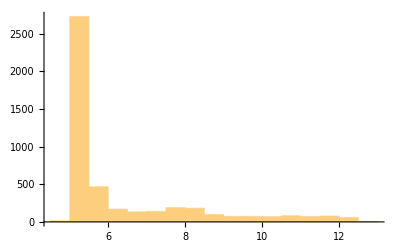

{4.70419,12.5952}

```mathematica
Histogram[Flatten[ImageData[id]]]
minmaxid=MinMax[Flatten[ImageData[id]]]
```

## Little Tests

Cases where we can find issues or cases where it’s working

#### Little Functions

```mathematica
pyrfi[ia_,ib_,row_,lvlmax_]:=Block[{pyrfia,pyrfib},
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvlmax];
pyrfib=pyrFuncGen[ImageData[ib][[row]],lvlmax];

Flatten[{pyrfia,pyrfib},{{2},{1},{3}}]
]
```

#### Little Test: Moving artificial image little by little

```mathematica
(*"OverConstrained"*)
(*"SemiConstrained"*)
(*"Constrained"*)
mode="Constrained";
e=0.01;
```

```mathematica
(* Check solution *)
ic=(*move[ia,-dv]*)ib;
lvlmin=1;
lvlmax=4;

res2ColorCode[test2[ia,ic,{lvlmin,lvlmax},e,mode],id]
res2ColorCode[test2[ia,ic,{lvlmax,lvlmax},e,mode],id];
res2ColorCode[test2[ia,ic,{lvlmin,lvlmin},e,mode],id];
```

{-Graphics-,-Graphics-,-Graphics-
297,-Graphics-
777,-Graphics-
868,-Graphics-
1841,-Graphics-
852}

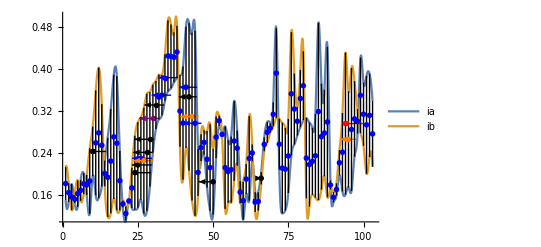

```mathematica
row=15;
pyrfiab=pyrfi[ia,ic,row,lvlmax];
lineTest[Range[1,103],{lvlmin,lvlmax},pyrfiab,e,mode]
```

```mathematica
(* Check solution *)
dv=max/2;
ic=(*move[ia,-dv]*)move[ib,dv];
lvlmin=1;
lvlmax=4;

res2ColorCode[test2[ia,ic,{lvlmin,lvlmax},e,mode],id]+{dv/max, 0,0,0,0,0,0}
res2ColorCode[test2[ia,ic,{lvlmax,lvlmax},e,mode],id];
res2ColorCode[test2[ia,ic,{lvlmin,lvlmin},e,mode],id];
```

{-Graphics-,-Graphics-,-Graphics-
1339,-Graphics-
444,-Graphics-
535,-Graphics-
1362,-Graphics-
955}

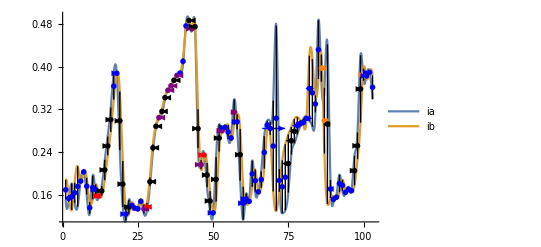

```mathematica
row=15;
pyrfiab=pyrfi[ia,ic,row,lvlmax];
lineTest[Range[1,103],{lvlmin,lvlmax},pyrfiab,e,mode]
```

```mathematica
e*2^(-lvlmin+1)
p=69;
ListAnimate[pixelTest[p,40,{lvlmin,lvlmax},pyrfiab,e,mode]]
```

0.01

#### Little test for sign left and middle

```mathematica
mode="ConstrainedSignLeftMiddle";
e=0.03;
```

```mathematica
(* Check solution *)
ic=(*move[ia,-dv]*)ib;
lvlmin=1;
lvlmax=4;

res2ColorCode[test2[ia,ic,{lvlmin,lvlmax},e,mode],id]
(*res2ColorCode[test2[ia,ic,{lvlmax,lvlmax},e,mode],id];*)
(*res2ColorCode[test2[ia,ic,{lvlmin,lvlmin},e,mode],id];*)
res2ColorCode[test2[ia,ic,{lvlmin,lvlmax},e,"Constrained"],id]
```

{-Graphics-,-Graphics-,-Graphics-
156,-Graphics-
3791,-Graphics-
288,-Graphics-
60,-Graphics-
340}

{-Graphics-,-Graphics-,-Graphics-
150,-Graphics-
3823,-Graphics-
268,-Graphics-
107,-Graphics-
287}

Show::gcomb: Could not combine the graphics objects in ….

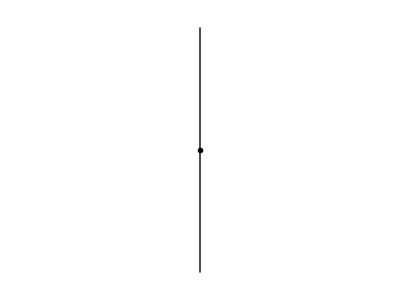
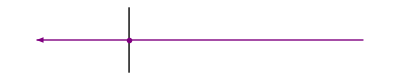
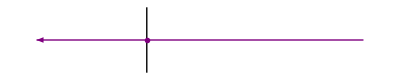
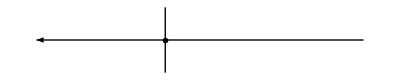
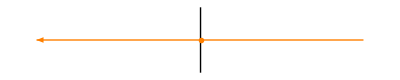
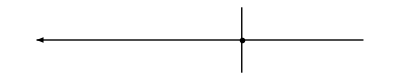
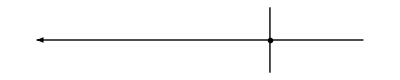
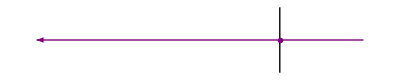
Show[signConditionalPlot[{InterpolatingFunction[…][x],InterpolatingFunction[…][x]},{x,1,103},All,All,{Filling→Axis,FillingStyle→RGBColor[0.88, 1, 0.88]},{Filling→Axis,FillingStyle→RGBColor[1, 0.85, 0.85]}],{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},ImageSize→Scaled[0.5]]

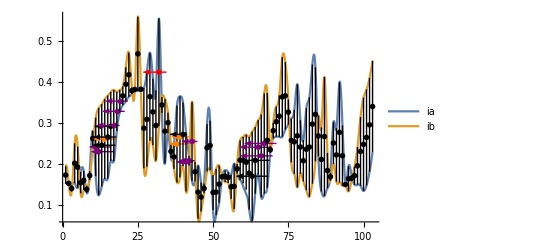

```mathematica
row=28;
pyrfiab=pyrfi[ia,ic,row,lvlmax];
lineTest[Range[1,103],{lvlmin,lvlmax},pyrfiab,e,mode]
lineTest[Range[1,103],{lvlmin,lvlmax},pyrfiab,e,"Constrained"]
```

```mathematica
e*2^(-lvlmin+1)
```

0.03

```mathematica
p=68;
ListAnimate[pixelTest[p,40,{lvlmin,lvlmax},pyrfiab,e,mode]]
(*ListAnimate[pixelTest[p,40,{lvlmin,lvlmax},pyrfiab,e,"Constrained"]]*)
```

```mathematica
findPrevNext[p0_,{dfline1_,dfline2_}]:=Block[{continue,notcontinue, resFunc, sumFunc,r1left,r2left},(
continue[p_]:=Sign[dfline1[p]*dfline2[p]]==-1;
notcontinue[p_]:=Sign[dfline1[p]*dfline2[p]]==1;
resFunc[p_]:=p-0.1;
sumFunc[p_]:=p+0.1;

r1left=NestWhile[resFunc,p0,continue,1,100];
r2left=NestWhile[resFunc,r1left,notcontinue,1,100];
rleft=(r2left+r1left)/2;

r1right=NestWhile[sumFunc,p0,continue,1,40];
r2right=NestWhile[sumFunc,r1right,notcontinue,1,100];
rright=(r2right+r1right)/2;

If[p0-rleft<rright-p0,rleft,rright]
)];
```

```mathematica
findPrevNext[p,pyrfiab[[3,All,2]]]
```

69.7

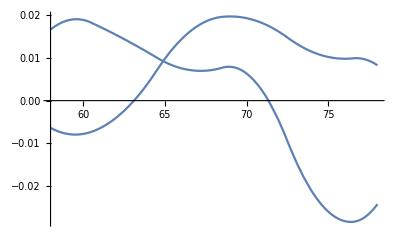

```mathematica
Plot[#[x]&/@pyrfiab[[3,All,2]],{x,p-10,p+10}]
```